```mathematica
<<Local`SrednickiInit`
```

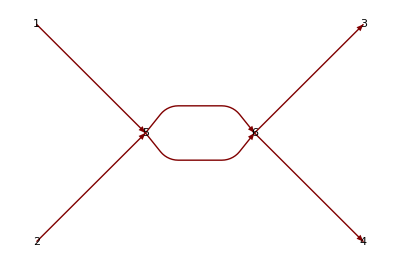

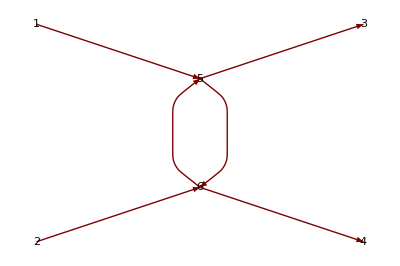

The O[λ^2] vertex correction diagrams.  The number of unique diagrams is determined by the number of different propagator values: 1-2, 1-3, 1-4.  The integral of the  O[λ^2] vertex function remains the same so only a factor of 3 is needed.

```mathematica
GraphPlot[{{1->5,k[1]},{2->5,k[2]},{5->6,q[1]},{5->6,q[2]},{6->3,k[3]},{6->4,k[4]}},VertexLabeling->True,DirectedEdges-> True,MultiedgeStyle->.5,VertexCoordinateRules->{1->{0,1},2->{0,-1},3->{3,1},4->{3,-1},5->{1,0},6->{2,0}} ]
GraphPlot[{{1->5,k[1]},{2->6,k[2]},{5->6,q[1]},{6->5,q[2]},{5->3,k[3]},{6->4,k[4]}},VertexLabeling->True,DirectedEdges-> True,MultiedgeStyle->.5,VertexCoordinateRules->{1->{0,1},2->{0,-1},3->{3,1},4->{3,-1},5->{1.5,.5},6->{1.5,-.5}} ]
"The O[λ^2] vertex correction diagrams.  The number of unique diagrams is determined by the number of different propagator values: 1-2, 1-3, 1-4.  The integral of the  O[λ^2] vertex function remains the same so only a factor of 3 is needed."//CC
```

```mathematica
"The vertex function is defined:"//CC
tmpv=I Subscript[V, 4][k[1],k[2],k[3],k[4]]->I Subscript[Z, λ] λ+(I λ)^2(1/I)^3 IntegralOp[{{q[1]}},1/(2π)^d Δ[q[1]]Δ[q[2]]]
"where:"//CC
sub=q[2]->k[1]+k[2]-q[1]
tmpv=tmpv/.sub;
"Substitute the free propagator:"//CC
DefPrint["e143",Δ[k_]->1/(k^2+m^2-ⅈ ϵ)]
"The vertex function becomes:"//CC
tmpv/.e143
"Using (14.9):"//CC
subd=Δ[a_]Δ[b_]->IntegralOp[{{x,0,1}},(x/Δ[q[1]]+(1-x)/Δ[q[2]]/.e143/.sub)^-2]
```

The vertex function is defined:

ⅈ V_4[k_1^1,k_2^2,k_3^3,k_4^4]→-ⅈ λ^2 IntegralOp[{{q_1^1}},(2 π)^-d Δ[q_1^1] Δ[q_2^2]]+ⅈ λ Z_λ

where:

q_2^2→k_1^1+k_2^2-q_1^1

Substitute the free propagator:

e143: Δ[k_]→1/(k^2+m^2-ⅈ ϵ)

The vertex function becomes:

ⅈ V_4[k_1^1,k_2^2,k_3^3,k_4^4]→-ⅈ λ^2 IntegralOp[{{q_1^1}},(2 π)^-d/((m^2-ⅈ ϵ+(k_1^1+k_2^2-q_1^1)^2) (m^2-ⅈ ϵ+(q_1^1)^2))]+ⅈ λ Z_λ

Using (14.9):

Δ[a_] Δ[b_]→IntegralOp[{{x,0,1}},1/(((1-x) (m^2-ⅈ ϵ+(k_1^1+k_2^2-q_1^1)^2)+x (m^2-ⅈ ϵ+(q_1^1)^2))^2)]

```mathematica
"Rearrange the denominator:"//CC
xDenom=(x/Δ[q[1]]+(1-x)/Δ[q[2]]/.e143/.sub/.ϵ->0)
xDenom//Expand;
xDenom//Collect[#,{q[1],k[_]}]&;
clist=CoefficientList[xDenom,q[1]];
"Find factor of form (q+x k)^2 :"//CC
sub1={x->x1+1,k[1]->kk-k[2]};
clist[[2]]=(clist[[2]]//Simplify)/.sub1;
clist[[1]]=(clist[[1]]-m^2//Simplify)+m^2/.sub1;
tmpc1=(clist[[1]]-(clist[[2]]/2)^2-m^2//Simplify)+m^2;
clist[[1]]=(clist[[2]]/2)^2;
tmpq2=Sum[clist[[i+1]] q[1]^i,{i,0,2}]//Factor;
xDenom=tmpq2+tmpc1/.x1->x-1/.kk->k[1]+k[2]
"So the propagator can be represented:"//CC
subdF2=subd/.IntegralOp[a_,b_]->IntegralOp[a,xDenom^-2]
```

Rearrange the denominator:

(1-x) (m^2+(k_1^1+k_2^2-q_1^1)^2)+x (m^2+(q_1^1)^2)

Find factor of form (q+x k)^2 :

m^2-(-1+x) x (k_1^1+k_2^2)^2+((-1+x) (k_1^1+k_2^2)+q_1^1)^2

So the propagator can be represented:

Δ[a_] Δ[b_]→IntegralOp[{{x,0,1}},1/((m^2-(-1+x) x (k_1^1+k_2^2)^2+((-1+x) (k_1^1+k_2^2)+q_1^1)^2)^2)]

```mathematica
"From the expression of V_4"//CC
tmp=tmpv/.subdF2/.IntegralOp[a_,b_]:>IntegralOpMoveNVarOut[a,b]/.IntegralOp[a_,IntegralOp[b_,c_]]:>IntegralOp[Flatten[{b,a},1],c];
tmp=Map[-ⅈ #&,tmp]//Expand
"redefine q[1] and introduce Dp"//CC
subq={q[1]->q[a]-(-1+x) (Subscript[k, 1]^1+Subscript[k, 2]^2),m^2->D+(-1+x) x (Subscript[k, 1]^1+Subscript[k, 2]^2)^2}
tmp=tmp/.IntegralOp[a_,b_]:>IntegralOp[a,(b/.subq)]/.q[1]->q[a];
"New vertex function:"//CC
tmpv1=tmp/.IntegralOp[{a_,b_},c_]->IntegralOp[{a},IntegralOp[{b},c]]
```

From the expression of V_4

V_4[k_1^1,k_2^2,k_3^3,k_4^4]→-(2 π)^-d λ^2 IntegralOp[{{x,0,1},{q_1^1}},1/((m^2-(-1+x) x (k_1^1+k_2^2)^2+((-1+x) (k_1^1+k_2^2)+q_1^1)^2)^2)]+λ Z_λ

redefine q[1] and introduce Dp

{q_1^1→-(-1+x) (k_1^1+k_2^2)+q_a^a,m^2→D+(-1+x) x (k_1^1+k_2^2)^2}

New vertex function:

V_4[k_1^1,k_2^2,k_3^3,k_4^4]→-(2 π)^-d λ^2 IntegralOp[{{x,0,1}},IntegralOp[{{q_a^a}},1/((D+(q_a^a)^2)^2)]]+λ Z_λ

```mathematica
"Using Wick rotation for the q[a,0] contour making the integral spherically symmetric and with (14.27) and (14.26)"//CC
DefPrint["e1427",IntegralOp[{{q}},1/(2 π)^d((q^2)^a)/((q^2+D)^b)]->(Gamma[b-a-d/2]Gamma[a+d/2])/((4 π)^(d/2)Gamma[b]Gamma[d/2])D^(-(b-a-d/2))]
DefPrint["e1426",Gamma[n_+x_]:>(-1)^-n/((-n)!)(1/x-γ+Sum[k^-1,{k,1,-n}])]
e1426z=Gamma[x_]->(Gamma[n+x]/.e1426/.n->0);

"For this case with dimensional regulation the integral becomes:"//CC
e1427/.a->0/.b->2/.q->q[a]/.IntegralOp[a_,b_]:>IntegralOpMoveNVarOut[a,b];
sub1427=Map[# (2 π)^d&,%];
sub1427=sub1427/.d->4-ε//Simplify
"also make the substitution:"//CC
subλ=λ->λ;   (μ̃)^(ε/2)(*Not substitution*)
"Substituting back into the expression for V_4 ."//CC
tmp=tmpv1/.sub1427/.e1426z/.subλ/.D->Dp[x]/.Subscript[Z, _]->Subscript[Z, λ];
tmpI=Extract[tmp,Position[tmp,IntegralOp[__]]][[1]];
tmpI=tmpI/.IntegralOp[a_,b_]:>IntegralOpMoveNVarOut[a,b]//PowerExpand;
xtmpI=tmpI/.A_^(1-ε/2):>(Series[A^(1-ε/2),{ε,0,1}]//Normal);
tmpv3=ReplacePart[tmp,Position[tmp,IntegralOp[__]]->tmpI]
```

Using Wick rotation for the q[a,0] contour making the integral spherically symmetric and with (14.27) and (14.26)

e1427: IntegralOp[{{q}},(2 π)^-d (q^2)^a (D+q^2)^-b]→(2^-d D^(a-b+d/2) π^(-d/2) Gamma[-a+b-d/2] Gamma[a+d/2])/(Gamma[b] Gamma[d/2])

e1426: Gamma[n_+x_]:>((-1)^-n (1/x-γ+∑_(k=1)^-n 1/k))/((-n)!)

For this case with dimensional regulation the integral becomes:

IntegralOp[{{q_a^a}},1/((D+(q_a^a)^2)^2)]→D^(-ε/2) π^(2-ε/2) Gamma[ε/2]

also make the substitution:

(μ̃)^(ε/2)

Substituting back into the expression for V_4 .

V_4[k_1^1,k_2^2,k_3^3,k_4^4]→-2^-d π^(2-d-ε/2) (-γ+2/ε) λ^2 IntegralOp[{{x,0,1}},Dp[x]^(-ε/2)]+λ Z_λ

```mathematica
tmp=tmpv4;
"Do integral to set on-shell condition:"//CC
tmp=tmp//PowerExpand;
tmpv4=tmp/.distributeInt/.IntegralOp[a_,b_]:>IntegralOpMoveNVarOut[a,b]/.IntegralOp[a_,1]->1
```

Do integral to set on-shell condition:

V_4[k_1^1,k_2^2,k_3^3,k_4^4]/λ→1+Cp+2^-d π^(2-d) λ (IntegralOp[{{x,0,1}},Log[Dp[x]]]+γ Log[e]+Log[π])

```mathematica
tmp=tmpv4;
{"Substituting:  ",
subDp={Dp[x]->m^2-(-1+x) x (Subscript[k, 1]^1+Subscript[k, 2]^2)^2,(k[1]+k[2])^2->s},"  And setting ",sub=s->4 m^2}//CC
tmp=tmp//.subDp/.IntegralOp[a_,b_]:>Integrate[b,Flatten[a],Assumptions->ε>0&&m>0&&s>0];
tmp=tmp/.sub
"The parameter setting V_4->λ suggests:"//CC
subCp=Solve[tmp[[2]]==1,Cp][[1]]//gatherLog[#]&//FullSimplify
subC/.subCp
```

{Substituting:  ,{Dp[x]→m^2-(-1+x) x (k_1^1+k_2^2)^2,(k_1^1+k_2^2)^2→s},  And setting ,s→4 m^2}

V_4[k_1^1,k_2^2,k_3^3,k_4^4]/λ→1+Cp+2^-d π^(2-d) λ (γ Log[e]+2 (-1+√2 ArcTanh[1/(√2)]+Log[m])+Log[π])

The parameter setting V_4->λ suggests:

{Cp→-2^-d π^(2-d) λ (-2+2 √2 ArcCoth[√2]+Log[e^γ m^2 π])}

C→(2^(1-d) π^(2-d) λ)/ε-2^-d π^(2-d) λ (-2+2 √2 ArcCoth[√2]+Log[e^γ m^2 π])

Problem 16.2

```mathematica
"The interaction term in the lagrangian for Prob.9.3 is"
Subscript[ℒ, int]->-1/4 Subscript[Z, λ] λ(SuperDagger[φ].φ)^2
```

The interaction term in the lagrangian for Prob.9.3 is

ℒ_int→-1/4 λ (φ^*.φ)^2 Z_λ

The graph of this vertex correction is presented with the arrow direction indicating particle or its conjugate.

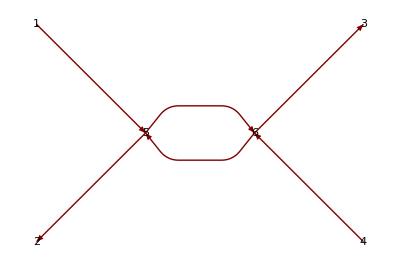

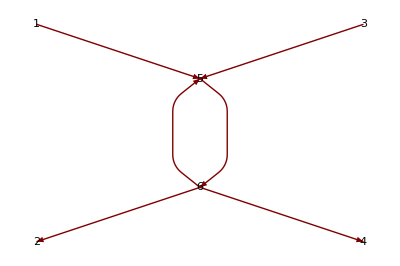

The O[λ^2] vertex correction diagrams.  The number of unique diagrams is determined by the number of different propagator values: 1-2, 1-3.  Additional interchange is not allowed by the conjugate-nonconjugate number requirement.  The integral of the  O[λ^2] vertex function remains the same so only a factor of 2 is needed.

```mathematica
"The graph of this vertex correction is presented with the arrow direction indicating particle or its conjugate."//CC
GraphPlot[{{1->5,φ[k[1]]},{5->2,SuperDagger[φ][k[2]]},{5->6,φ[q[1]]},{6->5,SuperDagger[φ][q[2]]},{6->3,φ[k[3]]},{4->6,SuperDagger[φ][k[4]]}},VertexLabeling->True,DirectedEdges-> True,MultiedgeStyle->.5,VertexCoordinateRules->{1->{0,1},2->{0,-1},3->{3,1},4->{3,-1},5->{1,0},6->{2,0}} ]
GraphPlot[{{1->5,φ[k[1]]},{6->2,SuperDagger[φ][k[2]]},{5->6,φ[q[1]]},{6->5,SuperDagger[φ][q[2]]},{3->5,SuperDagger[φ][k[3]]},{6->4,φ[k[4]]}},VertexLabeling->True,DirectedEdges-> True,MultiedgeStyle->.5,VertexCoordinateRules->{1->{0,1},2->{0,-1},3->{3,1},4->{3,-1},5->{1.5,.5},6->{1.5,-.5}} ]
"The O[λ^2] vertex correction diagrams.  The number of unique diagrams is determined by the number of different propagator values: 1-2, 1-3.  Additional interchange is not allowed by the conjugate-nonconjugate number requirement.  The integral of the  O[λ^2] vertex function remains the same so only a factor of 2 is needed."//CC
```